## Load packages

```mathematica
<<NFPackages`structuralMechanicsBook` // Quiet;
```

## Uniform load

### Summary

#### Simply-supported case:

1) Locate the middle of the beam and extend a vertical line down
2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.  Also, mark a point 60% (say about 50%) farther down along that vertical mid-line and call that point T.
3) Extend straight lines from point T to the beam supports.  These lines will be tangent to the displaced beam at the supports.
4) Draw two smooth lines, each starting horizontally at the middle or maximum displacement and meeting tangentially to the identified tangent line at either end.

#### Fixed-fixed case:

1) Locate the middle of the beam and extend a vertical line down
2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.
3) Extend lines from the maximum displacement to either end.
4) Draw two horizontal stubs at each end support.  The displaced beam will be tangent to these at both fixed ends.
5) Mark a location for x-coordinates of inflection points at about a fifth (actually, exactly 1/6(3-√3) or about 0.2113) times the length from either end.
6) The displaced inflection points almost meet the lines joining the support with the maximum displacements.  Actually, the displacements are about 5% farther down from those lines.  They are at exactly 2/9 (3+√3) times the distance to those lines from the horizontal. So, mark the approximate locations of the inflection points on both sides.
7) Draw a horizontal line between the two inflection points. This will be our new datum line. The deflected shape between the two inflection points is exactly that of the simply supported beam relative to this datum line. So, identify the point which the tangents at each side must meet.  This is about 60% further down than the chosen maximum displacement relative to the new datum.  Draw lines from that point to the inflection points to identify the tangent directions at each inflection point and sketch the displaced beam between the inflection point according to the directions of the simply supported beam.
8) At each end, draw a smooth curve tangent to the horizontal at the support and tangent to the directions identified at the inflection points.

#### Same rotary stiffness at each end with k > 1 case:

This is similar to the fixed-fixed case, but with some modifications:

1) Locate the middle of the beam and move a few percent (but always less than 5%) the length of the beam towards the less stiff side.  If we simply choose the middle, this will usually be visually good enough for a sketch.  Extend a vertical line down from that x-coordinate of the maximum displacement.
2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.
3) Extend lines from the maximum displacement to either support.
4) Mark a location for x-coordinates of inflection points.  For k = 1, 2, 3 at a particular support, it is about 0.13, 0.15 and 0.17 times the length from that support.  If we aim at 0.13 the length from each end for this usual range of values then, for a hand sketch, we will be visually fine. 0.13 the length may be targeted by aiming at half the quarter length.  So, locate x-coordinates of inflection points at each side at about half the quarter length away from each support.
Inflection point x-coordinate over length for different k’s:
(1 | 1/90 (45-15 √5) | 0.127322
3/2 | 1/144 (72-36 √2) | 0.146447
2 | 1/210 (105-7 √105) | 0.158435
3 | 1/378 (189-27 √21) | 0.172673)

5) The displacement is at a different distance farther down relative to the line joining the maximum displacement with the support.  For k = 1, 2, 3, it is about 33%, 25% and 20% further down than that line.  If we aim for about 25% down for this usual range of values, then, for a hand sketch, we will be visually fine.  So, mark the approximate locations of the inflection points on both sides at about a half the quarter length horizontally away from each support and 25% further down from the line joining the support with the maximum displacement.
Ratios discussed in this step for different k’s:
(1 | 16/63 (3+√5) | 1.3298
3/2 | 3/8 (2+√2) | 1.28033
2 | 4/81 (15+√105) | 1.24676
3 | 8/77 (7+√21) | 1.20338
4 | 28/351 (9+√33) | 1.1762
5 | (32 (33+√429))/1485 | 1.15744
∞ | 2/9 (3+√3) | 1.05157)

6) Draw a horizontal line between the two inflection points. This will be our new datum line. The deflected shape between the two inflection points is exactly that of the simply supported beam relative to this datum line. So, identify the point which the tangents at each side must meet.  This is about 60% further down than the chosen maximum displacement relative to the new datum.  Draw lines from that point to the inflection points to identify the tangent directions at each inflection point and sketch the displaced beam between the inflection point according to the directions of the simply supported beam.

7) At each end, draw a smooth curve tangent to the directions identified at the inflection points and at a slope that may extend either above or below the maximum displacement at the middle.  The slope to aim for depends on the value of the rotary stiffness factor ‘k’.  For k=0 we identified the steeper slope with a factor of 1.6. When k = 1.5, it is exactly the slope of the line joining the support with the maximum displacement.  For k larger than 1.5, the slope will be less steep and for k smaller it will be steeper.  Typical values are for k=1, 2, 3 which gives a ratio of 1.14, 0.89, 0.73.  In practice, choosing the slope slightly larger and slightly smaller than that of the line joining maximum displacement with support for k smaller and larger than 1.5 respectively will be visually sufficient for a sketch.

Ratio of value of extended tangent at the midpoint of beam divided by maximum displacement for different k’s (note: when k=0, this is the simply supported case):
(0 | 1.6
1 | 1.14286
1.5 | 1.
2 | 0.888889
3 | 0.727273
4 | 0.615385
5 | 0.533333)

#### Fixed-hinge case:

1) Locate where the maximum deflection occurs which is at about 7.8% the length away from the middle of the beam in the direction of the hinge support. Note that the maximum is closer to the hinge support. For an exact result, the maximum deflection is at 1/16 (15-√33) times the length away from the fixed support. Extend a vertical line down from that point.
2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.
3) Extend lines from the maximum displacement to either end.
4) Draw a horizontal stub at the fixed support.  The displaced beam will be tangent to this stub at that support.
5) Mark the x-coordinate for the inflection point at exactly a quarter (or 0.25 times) the length from the fixed support.
6) The displaced inflection point almost meets the line joining the support with the maximum displacements.  Actually, the displacement is about 4% farther down from the horizontal than that line.  It is at exactly 5/128 (-25+9 √33) times the distance from the horizontal to that line. So, mark the approximate location of the inflection point.
7) Draw an inclined line between the inflection point and the hinge. This will be our new datum line. The deflected shape relative to that datum is exactly that of the simply supported beam but rotated according to that inclination.  The steps are the same but relative to an inclined datum line.  So, sketch the displaced beam between the inflection point and hinge according to the directions of the simply supported beam. Note that the maximum displacement is not at the center of the inclined datum but at the point identified in step 1.
8) At the fixed end, draw a smooth curve tangent to the horizontal at the support and tangent to the direction identified at the inflection point.

#### General case:

If both sides have rotary stiffness in the range 1 to ∞ then this is sketched like the same rotary stiffness case but make the inflection point from the stiffer side a bit farther for k < 5 from its support.  If one side is fixed then the distance of the inflection point from that support is between 0.21 and 0.23 times the length which we take as practically 0.25 times the length.  Finally, the datum between inflection points will be generally inclined and drawing that is similar to what was described in the fixed-hinge case.

Distance of inflection point from support (one side spring and other has k = 1)
(1 | 0.127322
2 | 0.16497
3 | 0.182961
4 | 0.193497
5 | 0.200414
∞ | 0.233756)

Distance of inflection point from support (one side spring and other has k = ∞ or fixed)
(1 | 0.108756
2 | 0.143757
3 | 0.160973
4 | 0.171205
5 | 0.177983
∞ | 0.211325)

If one side is hinged then this will be similar to the fixed-hinge case but the x-coordinate of the sole inflection point will be very close to the same rotary stiffness case and the ratio of distance of the inflection point displacement relative to the line joining the maximum and spring end will vary so that for k = 1, 2, 3 it is 31%, 22% and 18% further down instead of only 4% for the fixed end case.  Visually, we may choose this as about 20% or a fifth for all cases for a decent sketch.

(0.01 | 1.59334
1 | 1.30904
2 | 1.22322
3 | 1.18021
4 | 1.15402
5 | 1.13632
∞ | 1.04301)

### Basic functions to be used

```mathematica
beamDeformedULMoment[ x, {kL, kR} ]
```

-(kL (6+4 kR))/(3 (4 (3+4 kR)+4 kL (4+4 kR)))+((3 (4+4 kR)+4 kL (5+4 kR)) x)/(8 (3+4 kR)+8 kL (4+4 kR))-x^2/2

```mathematica
beamDeformedULDisplacement[x,{kL, kR} ]
```

((-6-4 kR) x)/(12 (4 (3+4 kR)+4 kL (4+4 kR)))-(kL (6+4 kR) x^2)/(6 (4 (3+4 kR)+4 kL (4+4 kR)))+((3 (4+4 kR)+4 kL (5+4 kR)) x^3)/(12 (4 (3+4 kR)+4 kL (4+4 kR)))-x^4/24

```mathematica
secantBeamDeformedULDisplacement[ x_, {kL_, kR_} ] := secantBeamDeformedULSlope[ {kL, kR} ]  x
```

```mathematica
secantBeamDeformedULSlope[  {∞, ∞} ] := -1/192  
secantBeamDeformedULSlope[  {∞, kR_} ] := -(2+kR)/(192 (1+kR))  
secantBeamDeformedULSlope[  {kL_, ∞} ] := -(2+kL)/(192 (1+kL))  
secantBeamDeformedULSlope[  {kL_, kR_} ] := -(15+8 kR+4 kL (2+kR))/(192 (3+4 kR+4 kL (1+kR)))
```

```mathematica
tangentBeamDeformedULDisplacement[ x_, {kL_, kR_} ] := tangentBeamDeformedULSlope[  {kL, kR} ] x
```

```mathematica
tangentBeamDeformedULSlope[ {∞, ∞} ] := 0
tangentBeamDeformedULSlope[ {∞, kR_} ] := 0
tangentBeamDeformedULSlope[ {kL_, ∞} ] := -1/(48 (1+kL))
tangentBeamDeformedULSlope[  {kL_, kR_} ] := -(6+4 kR)/(12 (4 (3+4 kR)+4 kL (4+4 kR)))
```

### Graphics functions to be used

```mathematica
beamULDisplacementPrimitives[ kboth_, kcinf_, kc_, kLinf_, kL_, kRinf_, kR_, ulDisplacementScale_, showDisplacement_, showInflectionDimensions_ ] :=  makeMemberIllustration[ {{0, 0}, {1, 0}}, 
{"lineThicknessFactor" -> 0.75,

"displacementFunction" -> ( beamDeformedULDisplacement[ #, If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ]&), 
"displacementScale" ->  ulDisplacementScale }, 

Join[ 

If[showDisplacement,
Join[ {"showDisplacedQ" -> True,"lineColor" -> Gray, "member",
"inflectionPointLocation" -> beamDeformedULInflection[ If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ][[2]],
"lineColor" -> Red,
"inflectionPoint",
"inflectionPointLocation" -> beamDeformedULInflection[ If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ][[1]],
"lineColor" -> Red,
"inflectionPoint",
"lineColor" -> Black,
"dimensionInterval" -> {beamDeformedULInflection[ If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ][[2]], 1},
"dimensionText" -> With[ {v = 1 - beamDeformedULInflection[ If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ][[2]]},
(Style[ Row[ {NumberForm[  v// N, {5, 3} ], " L" } ], 14 ]) ]},

With[ {v = 1 - beamDeformedULInflection[ If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ][[2]]},
If[ NumericQ[ v ] && Abs[ v ] > 10^-2, If[ showInflectionDimensions, {"dimension"}, {}], {} ] ],

{
"dimensionInterval" -> {0, beamDeformedULInflection[ If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ][[1]]},
"dimensionText" -> 
With[ {v = beamDeformedULInflection[ If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ][[1]]},
(Style[ Row[ {NumberForm[  v // N, {5, 3} ], " L" } ], 14 ]) ]
},

With[ {v = beamDeformedULInflection[ If[ kboth, {If[ kcinf, ∞, kc],If[ kcinf, ∞, kc]},  {If[ kLinf, ∞, kL], If[ kRinf, ∞, kR]} ] ][[1]]},
If[ Abs[ v ] > 10^-2, If[ showInflectionDimensions, {"dimension"}, {}], {} ] ]
],
{}
],

{
"lineColor" -> Directive[ Gray],"lineThicknessFactor" -> 0.25,  "showDisplacedQ" -> False, "member"
}
],

 
Join[ 
{"lineThicknessFactor" -> 0.5, "lineColor" -> Directive[ Black, Opacity[0.5], PointSize[0.01] ]},
{If[ kboth, If[ kcinf, "fixed", "hinge" ], If[ kLinf, "fixed", "hinge" ] ]},
If[ kboth, If[ kc > 0 && kcinf =!= True, { "spring"}, {} ], If[ kL > 0 && kLinf =!= True, { "spring"}, {} ] ],
If[ kboth, 
{"labelText" -> If[ kcinf === True || kc == 0, "", Style[ Row[ {kc, "×4EI/L"} ], 14 ] ], "labelOffsetVector" -> {-0.15, 0.15}, "label"},
{"labelText" -> If[ kLinf === True || kL == 0, "", Style[ Row[ {kL, "×4EI/L"} ], 14 ] ], "labelOffsetVector" -> {-0.15, 0.15}, "label"}
]
],

 
Join[ 
{"lineThicknessFactor" -> 0.5, "lineColor" -> Directive[ Black, Opacity[0.5], PointSize[0.01] ]},
{If[ kboth, If[ kcinf, "fixed", "hinge" ], If[ kRinf, "fixed", "hinge" ] ]},
If[ kboth, If[ kc > 0 && kcinf =!= True, { "spring"}, {} ], If[ kR > 0 && kRinf =!= True, { "spring"}, {} ] ],
If[ kboth, 
{"labelText" -> If[ kcinf === True || kc == 0, "", Style[ Row[ {kc, "×4EI/L"} ], 14 ] ], "labelOffsetVector" -> {0.15, 0.15}, "label"},
{"labelText" -> If[ kRinf === True || kR == 0, "", Style[ Row[ {kR, "×4EI/L"} ], 14 ] ], "labelOffsetVector" -> {0.15, 0.15}, "label"}
]
] ]
```

### Facts about simply supported case

#### Maximum displacement versus extended line

```mathematica
beamDeformedULDisplacement[1/2,{kL,kR} ]
```

-1/384+(-6-4 kR)/(24 (4 (3+4 kR)+4 kL (4+4 kR)))-(kL (6+4 kR))/(24 (4 (3+4 kR)+4 kL (4+4 kR)))+(3 (4+4 kR)+4 kL (5+4 kR))/(96 (4 (3+4 kR)+4 kL (4+4 kR)))

```mathematica
ratioMidVersusExtendedLine[ kL_, kR_ ] := beamDeformedULDisplacement[1/2,{kL,kR} ] /tangentBeamDeformedULDisplacement[ 1/2, {kL, kR} ]  // FullSimplify // ExpandNumerator // ExpandDenominator
```

```mathematica
ratioMidVersusExtendedLine[ kL, kR ]
```

(15+8 kL+8 kR+4 kL kR)/(24+16 kR)

```mathematica
NMinimize[ {ratioMidVersusExtendedLine[kL, kR], kL ≥ 0 && kR ≥ 0}, {kL, kR}]
```

{0.5,{kL→-7.01066×10^-50,kR→4.25048×10^7}}

```mathematica
Table[ {k, ratioMidVersusExtendedLine[k, k ] //N// NumberForm[ #, {5, 3}]& }, {k, {0, 1, 1.5, 2, 3}}]
```

{{0,0.625},{1,0.875},{1.5,1.000},{2,1.125},{3,1.375}}

```mathematica
NSolve[ ratioMidVersusExtendedLine[k, k ] == 1, {k, k} ]
```

{{k→1.5}}

#### Initial slope versus secant slope

```mathematica
ratioTangentSlopeVersusSecantSlope[ kL_, kR_ ] := beamDeformedULRotation[0,{kL,kR} ] /secantBeamDeformedULSlope[  {kL, kR} ]  // FullSimplify // ExpandNumerator // ExpandDenominator
```

```mathematica
ratioTangentSlopeVersusSecantSlope[ kL, kR ]
```

(24+16 kR)/(15+8 kL+8 kR+4 kL kR)

```mathematica
ratioTangentSlopeVersusSecantSlope[ 0, 0 ]
```

8/5

```mathematica
Solve[ ratioTangentSlopeVersusSecantSlope[ k, k ] == 1, {k, k} ]
```

{{k→3/2}}

#### Inflection point location

```mathematica
Table[ {k, beamDeformedULInflection[ {k, k} ][[1]] // N}, {k, {0, 1, 1.5, 2, 3, ∞}}] // MatrixForm
```

(0 | 0.
1 | 0.127322
1.5 | 0.146447
2 | 0.158435
3 | 0.172673
∞ | 0.211325)

```mathematica
Module[ {kList, mat},
kList = {0, 1, 1.5, 2, 3, ∞};
mat = ConstantArray[ 0, {Length[ kList] + 1, Length[ kList ] + 1} ];
mat[[ 2;;-1, 2;;-1 ]] = Table[ beamDeformedULInflection[ {kL, kR} ][[1]] // N, {kL, kList}, {kR, kList}];
mat[[ 1, 2;;-1]] = kList;
mat[[ 2;;-1, 1 ]] = kList;
mat
] // Grid
```

0 | 0 | 1 | 1.5 | 2 | 3 | ∞
0 | 0. | 0. | 0. | 0. | 0. | 0.
1 | 0.142857 | 0.127322 | 0.123865 | 0.121492 | 0.118445 | 0.108756
1.5 | 0.166667 | 0.150181 | 0.146447 | 0.143868 | 0.140542 | 0.129844
2 | 0.181818 | 0.16497 | 0.16111 | 0.158435 | 0.154974 | 0.143757
3 | 0.2 | 0.182961 | 0.179004 | 0.17625 | 0.172673 | 0.160973
∞ | 0.25 | 0.233756 | 0.229844 | 0.22709 | 0.223473 | 0.211325

```mathematica
With[ {kRmin = 1, kRmax = 3, kLmin = 1, kLmax = 3},
NIntegrate[ (beamDeformedULInflection[ {kL, kR} ][[1]])/((kRmax - kRmin) * (kLmax - kLmin)), {kR, kRmin, kRmax}, {kL, kLmin, kLmax} ] ]
```

0.155897

### Illustration

```mathematica
Manipulate[
{
Which[ kboth === True,
If[ kcinf, {kLn, kRn} = {∞, ∞}, {kLn, kRn} = {kc, kc} ],
kboth =!= True,
If[  kLinf, kLn = ∞, kLn = kL ]; If[  kRinf, kRn = ∞, kRn = kR ]
];

{beamULDisplacementPrimitives[ kboth, kcinf, kc, kLinf, kL, kRinf, kR, amp, True, False ]},
{Thickness[ 0.004],Green, Line[ {{0, 0},{1/2,  amp beamDeformedULDisplacement[ 1/2,{ kLn, kRn} ]}}],
Thickness[ 0.004],Purple,Line[ {{0, 0},{1/2,  amp tangentBeamDeformedULDisplacement[ 1/2, {kLn, kRn}]}}],
Blue, HalfLine[ {{1/2, 0}, {1/2, -1} } ]
}
} // Graphics,

{{amp, 50}, 10, 100, 10},
Delimiter,
Grid[ {{ Control[ {{kL, 0, Dynamic[ Row[ {"kL = ", kL }]]}, 0, 3, 0.25} ], Control[ {{kLinf, False}, {True, False}}]}}],
Grid[ {{ Control[ {{kR, 0,  Dynamic[ Row[ {"kR = ", kR }]]}, 0, 3, 0.25} ], Control[ {{kRinf, False}, {True, False}}]}}],
Delimiter,
Control[ {{kboth, False}, {True, False}} ],Grid[ {{ Control[ {{kc, 0,  Dynamic[ Row[ {"kc = ", kc }]]}, 0, 3, 0.25} ], Control[ {{kcinf, False}, {True, False}}]}}]

]
```

### Basic notes

#### Fixed-hinge case

```mathematica
ArgMax[ { -beamDeformedULDisplacement[ x, {0, ∞} ], 0 ≤ x ≤ 1 }, x ]
```

1/16 (1+√33)

```mathematica
ArgMax[ { -beamDeformedULDisplacement[ x, {0, ∞} ], 0 ≤ x ≤ 1 }, x ] *{1, 1.} // FullSimplify
```

{1/16 (1+√33),0.421535}

Location of max displacement:  {1/16 (1+√33),0.421535}
Location of inflection point:  0.25 L from fixed

```mathematica
xIfixedHinge = beamDeformedULInflection[ {∞, 0} ][[1]]
```

1/4

```mathematica
beamDeformedULMaxDeflectionLocAndMax[ {1, 0} ] // N
```

{0.532966,-0.00860577}

```mathematica
xmaxfixedHinge = ArgMax[ { -beamDeformedULDisplacement[ x, {∞, 0} ], 0 ≤ x ≤ 1 }, x ]
```

1/16 (15-√33)

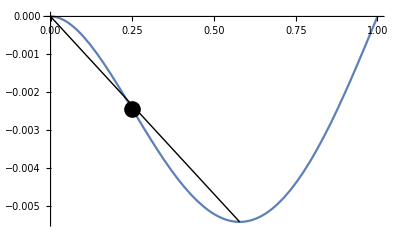

```mathematica
Plot[ beamDeformedULDisplacement[ x, {∞, 0} ], {x, 0, 1},
Epilog -> { PointSize[0.03], Point[ {xIfixedHinge, beamDeformedULDisplacement[ xIfixedHinge, {∞, 0} ]}],
Line[ {{0, 0}, {xmaxfixedHinge,beamDeformedULDisplacement[ xmaxfixedHinge, {∞, 0} ]} } ]}
]
```

```mathematica
beamDeformedULDisplacement[ xIfixedHinge, {∞, 0} ]/((1/xmaxfixedHinge) beamDeformedULDisplacement[ xmaxfixedHinge, {∞, 0} ] * xIfixedHinge) * {1, 1.} // FullSimplify
```

{5/128 (-25+9 √33),1.04301}

#### General spring-spring case

```mathematica
ArgMin[ {beamDeformedULDisplacement[ x, {∞, 1}], 0 ≤ x ≤ 1}, x ] // N
```

0.548938

```mathematica
xIspringSpring[kL_, kR_ ] := beamDeformedULInflection[ {kL, kR} ][[1]]
```

```mathematica
xmaxspringSpring[kL_, kR_] := ArgMax[ { -beamDeformedULDisplacement[ x, {kL, kR} ], 0 ≤ x ≤ 1 }, x ]
```

```mathematica
Table[ {kL, (beamDeformedULDisplacement[ xIspringSpring[kL, 1], {kL, 1} ]/((1/xmaxspringSpring[kL, 1]) beamDeformedULDisplacement[ xmaxspringSpring[kL, 1], {kL, 1} ] * xIspringSpring[kL, 1]) // N)}, {kL, {0.01, 1, 2, 3,4, 5, ∞}}] // MatrixForm
```

(0.01 | 1.60898
1 | 1.3298
2 | 1.24083
3 | 1.19561
4 | 1.16788
5 | 1.14906
∞ | 1.0486)

```mathematica
Table[ {kL, beamDeformedULInflection[ {kL, 1}][[1]]//N}, {kL, { 1, 2, 3,4, 5, ∞}}] // MatrixForm
```

(1 | 0.127322
2 | 0.16497
3 | 0.182961
4 | 0.193497
5 | 0.200414
∞ | 0.233756)

```mathematica
Table[ {kL, beamDeformedULInflection[ {kL, ∞}][[1]]//N}, {kL, { 1, 2, 3,4, 5, ∞}}] // MatrixForm
```

(1 | 0.108756
2 | 0.143757
3 | 0.160973
4 | 0.171205
5 | 0.177983
∞ | 0.211325)

#### General spring-hinge case

```mathematica
Table[ {k, (beamDeformedULDisplacement[ xIspringHinge[k], {k, 0} ]/((1/xmaxspringHinge[k]) beamDeformedULDisplacement[ xmaxspringHinge[k], {k, 0} ] * xIspringHinge[k]) // N)}, {k, {0.01, 1, 2, 3,4, 5, ∞}}] // MatrixForm
```

(0.01 | 1.59334
1 | 1.30904
2 | 1.22322
3 | 1.18021
4 | 1.15402
5 | 1.13632
∞ | 1.04301)

```mathematica
Table[ {k, xIspringHinge[k ] // N}, {k, {1, 2, 3, 4, 5, ∞}}] // MatrixForm
```

(1 | 0.142857
2 | 0.181818
3 | 0.2
4 | 0.210526
5 | 0.217391
∞ | 0.25)

```mathematica
xIspringHinge[k_] := beamDeformedULInflection[ {k, 0} ][[1]]
```

```mathematica
xmaxspringHinge[k_] := ArgMax[ { -beamDeformedULDisplacement[ x, {k, 0} ], 0 ≤ x ≤ 1 }, x ]
```

```mathematica
xIspringHinge[ 1.]
```

0.142857

```mathematica
x
```

```mathematica
Table[ {k, (beamDeformedULDisplacement[ xIspringHinge[k], {k, 0} ]/((1/xmaxspringHinge[k]) beamDeformedULDisplacement[ xmaxspringHinge[k], {k, 0} ] * xIspringHinge[k]) // N)}, {k, {0.01, 1, 2, 3, ∞}}] // MatrixForm
```

(0.01 | 1.59334
1 | 1.30904
2 | 1.22322
3 | 1.18021
∞ | 1.04301)

#### Fixed-fixed

```mathematica
xIfixed = beamDeformedULInflection[ {∞, ∞} ][[1]]
```

1/6 (3-√3)

```mathematica
beamDeformedULDisplacement[ xIfixed, {∞, ∞} ]/(2 beamDeformedULDisplacement[ 1/2, {∞, ∞} ] * xIfixed) * {1, 1.} // FullSimplify
```

{2/9 (3+√3),1.05157}

```mathematica
2 beamDeformedULDisplacement[ 1/2, {∞, ∞} ] * xIfixed / LinearModelFit[ {{0, 0}, {1/2,beamDeformedULDisplacement[ 1/2, {∞, ∞} ]} }, {1, x}, x ][ xIfixed ]
```

1.

```mathematica
2 beamDeformedULDisplacement[ 1/2, {∞, ∞} ] * xIfixed
```

(-3+√3)/1152

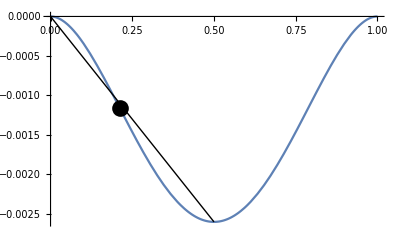

```mathematica
Plot[ beamDeformedULDisplacement[x, {∞, ∞} ], {x, 0, 1},
Epilog -> { PointSize[0.03], Point[ {xIfixed, beamDeformedULDisplacement[ xIfixed, {∞, ∞} ]}],
Line[ {{0, 0}, {1/2,beamDeformedULDisplacement[ 1/2, {∞, ∞} ]} } ]} ]
```

#### Same rotary stiffness at each side

```mathematica
Table[ {k, beamDeformedULRotation[ 0, {k, k}]/(2 beamDeformedULDisplacement[ 1/2, {k, k} ]) //N// Simplify},
{k, {0, 1,1.5, 2, 3, 4, 5}}] // MatrixForm
```

(0 | 1.6
1 | 1.14286
1.5 | 1.
2 | 0.888889
3 | 0.727273
4 | 0.615385
5 | 0.533333)

```mathematica
xIspringSpring[kL_, kR_ ] := beamDeformedULInflection[ {kL, kR} ][[1]]
```

```mathematica
Table[ {k, Sequence @@ (beamDeformedULDisplacement[ xIspringSpring[k, k], {k, k} ]/(2 beamDeformedULDisplacement[ 1/2, {k, k} ] * xIspringSpring[k, k]) * {1, 1.} // FullSimplify)}, {k, {1, 3/2, 2, 3, 4, 5, ∞}} ] // MatrixForm
```

(1 | 16/63 (3+√5) | 1.3298
3/2 | 3/8 (2+√2) | 1.28033
2 | 4/81 (15+√105) | 1.24676
3 | 8/77 (7+√21) | 1.20338
4 | 28/351 (9+√33) | 1.1762
5 | (32 (33+√429))/1485 | 1.15744
∞ | 2/9 (3+√3) | 1.05157)

```mathematica
Table[ {k, beamDeformedULDisplacement[ xIfixed, {k, k} ] // N}, {k, {1, 3/2, 2, 3, 4, 5, ∞}} ]
```

```mathematica
Table[ {k, beamDeformedULInflection[ {k, k}][[1]], beamDeformedULInflection[ {k, k}][[1]] // N}, {k, {1, 3/2, 2, 3} } ] // MatrixForm
```

(1 | 1/90 (45-15 √5) | 0.127322
3/2 | 1/144 (72-36 √2) | 0.146447
2 | 1/210 (105-7 √105) | 0.158435
3 | 1/378 (189-27 √21) | 0.172673)

### Preparing files for comparisons

```mathematica
Export[ makeMediaFileName[ { $PAABFSourceMathematica, $PAABFTypeMovie}, 
$PAABFScreenMainFull,  
"UL hinge-hinge",
"MOV"
],
figs ]
```

/Users/Nabil Fares 2/Desktop/MM-M1-UL hinge-hinge-160904.MOV

```mathematica
Export[ makeMediaFileName[ { $PAABFSourceMathematica, $PAABFTypeMovie}, 
$PAABFScreenMainFull,  
"UL fixed-fixed",
"MOV"
],
figs ]
```

/Users/Nabil Fares 2/Desktop/MM-M1-UL fixed-fixed-160904.MOV

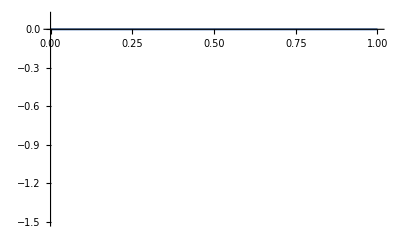
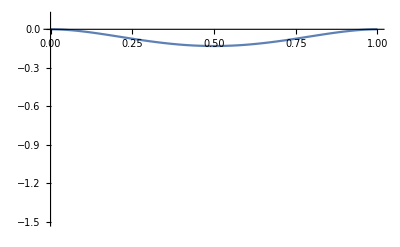
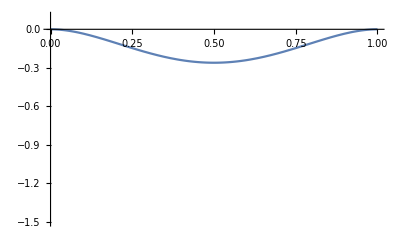
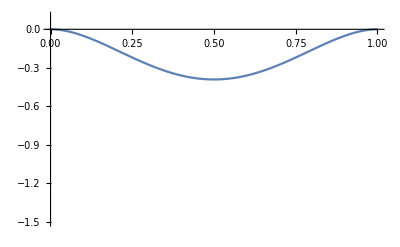
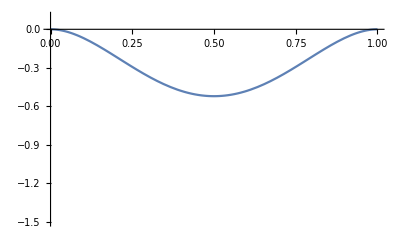
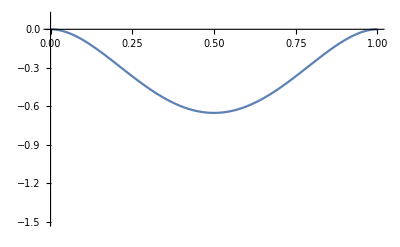
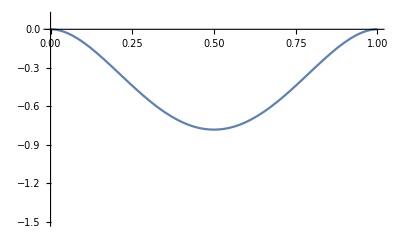
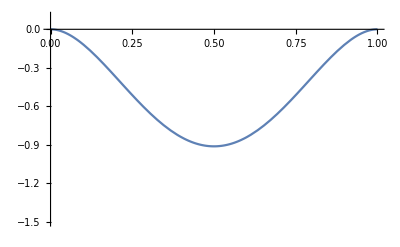

```mathematica
figs = Table[ Plot[ amp beamDeformedULDisplacement[ x, {∞, ∞}], {x, 0, 1}, PlotRange -> {-1.5, 0.1}], {amp, 0, 500, 50}]
```

## Point force

### Summary

#### Simply-supported case:

Point force in the middle:
1) Locate the middle of the beam and extend a vertical line down
2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.  Also, mark a point 50% (it is exactly 50%) farther down along that vertical mid-line and call that point T.
3) Extend straight lines from point T to the beam supports.  These lines will be tangent to the displaced beam at the supports.
4) Draw two smooth lines, each starting horizontally at the middle or maximum displacement and meeting tangentially to the identified tangent line at either end.

Point force not in the middle:
1) Locate the middle of the beam and move at most 7.7% closer to the point force and extend a vertical line down (in construction, if xF < 0.25 we could move it about a quarter of a quarter closer to the force location, otherwise use half of that quarter of a quarter which is probably within the visual margin of error)

2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.  
For the side farther from support, mark a point Tfarther 50% lower and for the side closer to the support, mark a point Tnearer 60% lower.  A small table is shown below:
Position of point force from support versus ratio of tangential to maximum displacement:
       xF              ratio
(0.0001 | 2.19582
0.1 | 1.91928
0.25 | 1.65659
0.3 | 1.59999
0.4 | 1.52541
0.5 | 1.5
0.75 | 1.5
0.9999 | 1.5)

3) Extend straight lines from point Tnearer to the nearer support and from point Tfarther to the farther support.  These lines will be tangent to the displaced beam at the supports.
4) Draw two smooth lines, each starting horizontally at the middle or maximum displacement and meeting tangentially to the identified tangent line at either end.

#### Fixed-fixed case: *

1) Locate the middle of the beam.  If the force is at the middle then that’s the x-coordinate of the maximum displacement. Otherwise, move at most 16.7% the length closer to the load point and extend a vertical line down. In construction, if xF = 0.25 we need to move it about 10% which is visually about half a quarter away from the force location.  The table shows location of maximum displacement versus location of force from the left:
      xF    x at max δ
(0 | "0.167"
0.1 | "0.143"
0.2 | "0.115"
0.25 | "0.100"
0.3 | "0.083"
0.4 | "0.045"
0.5 | "0.000")

2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.

3) Extend lines from the maximum displacement to either end.
4) Draw two horizontal stubs at each end support.  The displaced beam will be tangent to these at both fixed ends.

5) Mark a location for x-coordinates of inflection points.  If point force is at the middle, then they are at 0.25 the length from each side.  Otherwise, use the table below:

(0 | {"0.000","0.667"}
0.1 | {"0.083","0.679"}
0.2 | {"0.143","0.692"}
0.25 | {"0.167","0.700"}
0.3 | {"0.188","0.708"}
0.4 | {"0.222","0.727"}
0.5 | {"0.250","0.750"})

6) The displaced inflection points almost meet the lines joining the support with the maximum displacements.  Actually, the displacements are about 5% farther down from those lines.  They are at exactly 2/9 (3+√3) times the distance to those lines from the horizontal. So, mark the approximate locations of the inflection points on both sides.
7) Draw a horizontal line between the two inflection points. This will be our new datum line. The deflected shape between the two inflection points is exactly that of the simply supported beam relative to this datum line. So, identify the point which the tangents at each side must meet.  This is about 60% further down than the chosen maximum displacement relative to the new datum.  Draw lines from that point to the inflection points to identify the tangent directions at each inflection point and sketch the displaced beam between the inflection point according to the directions of the simply supported beam.
8) At each end, draw a smooth curve tangent to the horizontal at the support and tangent to the directions identified at the inflection points.

#### Same rotary stiffness at each end with k > 1 case: *

This is similar to the fixed-fixed case, but with some modifications:

1) Locate the middle of the beam and move a few percent (but always less than 5%) the length of the beam towards the less stiff side.  If we simply choose the middle, this will usually be visually good enough for a sketch.  Extend a vertical line down from that x-coordinate of the maximum displacement.
2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.
3) Extend lines from the maximum displacement to either support.
4) Mark a location for x-coordinates of inflection points.  For k = 1, 2, 3 at a particular support, it is about 0.13, 0.15 and 0.17 times the length from that support.  If we aim at 0.13 the length from each end for this usual range of values then, for a hand sketch, we will be visually fine. 0.13 the length may be targeted by aiming at half the quarter length.  So, locate x-coordinates of inflection points at each side at about half the quarter length away from each support.
Inflection point x-coordinate over length for different k’s:
(1 | 1/90 (45-15 √5) | 0.127322
3/2 | 1/144 (72-36 √2) | 0.146447
2 | 1/210 (105-7 √105) | 0.158435
3 | 1/378 (189-27 √21) | 0.172673)

5) The displacement is at a different distance farther down relative to the line joining the maximum displacement with the support.  For k = 1, 2, 3, it is about 33%, 25% and 20% further down than that line.  If we aim for about 25% down for this usual range of values, then, for a hand sketch, we will be visually fine.  So, mark the approximate locations of the inflection points on both sides at about a half the quarter length horizontally away from each support and 25% further down from the line joining the support with the maximum displacement.
Ratios discussed in this step for different k’s:
(1 | 16/63 (3+√5) | 1.3298
3/2 | 3/8 (2+√2) | 1.28033
2 | 4/81 (15+√105) | 1.24676
3 | 8/77 (7+√21) | 1.20338
4 | 28/351 (9+√33) | 1.1762
5 | (32 (33+√429))/1485 | 1.15744
∞ | 2/9 (3+√3) | 1.05157)

6) Draw a horizontal line between the two inflection points. This will be our new datum line. The deflected shape between the two inflection points is exactly that of the simply supported beam relative to this datum line. So, identify the point which the tangents at each side must meet.  This is about 60% further down than the chosen maximum displacement relative to the new datum.  Draw lines from that point to the inflection points to identify the tangent directions at each inflection point and sketch the displaced beam between the inflection point according to the directions of the simply supported beam.

7) At each end, draw a smooth curve tangent to the directions identified at the inflection points and at a slope that may extend either above or below the maximum displacement at the middle.  The slope to aim for depends on the value of the rotary stiffness factor ‘k’.  For k=0 we identified the steeper slope with a factor of 1.6. When k = 1.5, it is exactly the slope of the line joining the support with the maximum displacement.  For k larger than 1.5, the slope will be less steep and for k smaller it will be steeper.  Typical values are for k=1, 2, 3 which gives a ratio of 1.14, 0.89, 0.73.  In practice, choosing the slope slightly larger and slightly smaller than that of the line joining maximum displacement with support for k smaller and larger than 1.5 respectively will be visually sufficient for a sketch.

Ratio of value of extended tangent at the midpoint of beam divided by maximum displacement for different k’s (note: when k=0, this is the simply supported case):
(0 | 1.6
1 | 1.14286
1.5 | 1.
2 | 0.888889
3 | 0.727273
4 | 0.615385
5 | 0.533333)

#### Fixed-hinge case: *

1) Locate where the maximum deflection occurs which is at about 7.8% the length away from the middle of the beam in the direction of the hinge support. Note that the maximum is closer to the hinge support. For an exact result, the maximum deflection is at 1/16 (15-√33) times the length away from the fixed support. Extend a vertical line down from that point.
2) Along that line, choose the maximum displacement that you want to show and mark a horizontal stub which we need to meet tangentially.
3) Extend lines from the maximum displacement to either end.
4) Draw a horizontal stub at the fixed support.  The displaced beam will be tangent to this stub at that support.
5) Mark the x-coordinate for the inflection point at exactly a quarter (or 0.25 times) the length from the fixed support.
6) The displaced inflection point almost meets the line joining the support with the maximum displacements.  Actually, the displacement is about 4% farther down from the horizontal than that line.  It is at exactly 5/128 (-25+9 √33) times the distance from the horizontal to that line. So, mark the approximate location of the inflection point.
7) Draw an inclined line between the inflection point and the hinge. This will be our new datum line. The deflected shape relative to that datum is exactly that of the simply supported beam but rotated according to that inclination.  The steps are the same but relative to an inclined datum line.  So, sketch the displaced beam between the inflection point and hinge according to the directions of the simply supported beam. Note that the maximum displacement is not at the center of the inclined datum but at the point identified in step 1.
8) At the fixed end, draw a smooth curve tangent to the horizontal at the support and tangent to the direction identified at the inflection point.

#### General case: *

If both sides have rotary stiffness in the range 1 to ∞ then this is sketched like the same rotary stiffness case but make the inflection point from the stiffer side a bit farther for k < 5 from its support.  If one side is fixed then the distance of the inflection point from that support is between 0.21 and 0.23 times the length which we take as practically 0.25 times the length.  Finally, the datum between inflection points will be generally inclined and drawing that is similar to what was described in the fixed-hinge case.

Distance of inflection point from support (one side spring and other has k = 1)
(1 | 0.127322
2 | 0.16497
3 | 0.182961
4 | 0.193497
5 | 0.200414
∞ | 0.233756)

Distance of inflection point from support (one side spring and other has k = ∞ or fixed)
(1 | 0.108756
2 | 0.143757
3 | 0.160973
4 | 0.171205
5 | 0.177983
∞ | 0.211325)

If one side is hinged then this will be similar to the fixed-hinge case but the x-coordinate of the sole inflection point will be very close to the same rotary stiffness case and the ratio of distance of the inflection point displacement relative to the line joining the maximum and spring end will vary so that for k = 1, 2, 3 it is 31%, 22% and 18% further down instead of only 4% for the fixed end case.  Visually, we may choose this as about 20% or a fifth for all cases for a decent sketch.

(0.01 | 1.59334
1 | 1.30904
2 | 1.22322
3 | 1.18021
4 | 1.15402
5 | 1.13632
∞ | 1.04301)

### Basic functions to be used

```mathematica
beamDeformedPFMoment[x,{kL,kR},xF]
```

Piecewise[{{1/(3+4 kR+4 kL (1+kR))(1-xF) ((3+4 kR+4 kL (1+kR)) x-4 kL (1+kR) xF-2 (kL+kR+4 kL kR) x xF^2+2 xF (-kR x+kL (2 (1+kR) x+xF+2 kR xF))), x≥0&&x<xF}, {(xF (3+4 kR-3 (1+2 kR) x+2 kL (3+4 kR) xF+2 (kL+kR+4 kL kR) x xF^2-2 kL (1+2 kR) xF (3 x+xF)))/(3+4 kR+4 kL (1+kR)), 1≥x&&x≥xF}, {0, True}}]

```mathematica
beamDeformedPFDisplacement[x,{kL, kR}, xF ]
```

Piecewise[{{1/(6 (3+4 kR+4 kL (1+kR)))x (1-xF) ((3+4 kR+4 kL (1+kR)) x^2-6 (1+kR) xF-12 kL (1+kR) x xF+3 (1+2 kR) xF^2-2 (kL+kR+4 kL kR) x^2 xF^2+2 x xF (-kR x+kL (2 x+2 kR x+3 xF+6 kR xF))), 0≤x<xF}, {-1/(6 (3+4 kR+4 kL (1+kR)))(1-x) xF (6 (1+kR) x-(3+6 kR) x^2+12 kL (1+kR) x xF-(3+4 kR+4 kL (1+kR)) xF^2+2 (kL+kR+4 kL kR) x^2 xF^2-2 x xF (-kR xF+kL ((3+6 kR) x+2 (1+kR) xF))), xF≤x≤1}, {0, True}}]

```mathematica
beamDeformedPFSlopes[{kL, kR}, xF ]
```

{-((-1+xF) xF (-2+2 kR (-1+xF)+xF))/(6+8 kR+8 kL (1+kR)),-((-1+xF) xF (1+xF+2 kL xF))/(6+8 kR+8 kL (1+kR))}

```mathematica
xAtMaxDisplacementPF[ {kL_, kR_}, xF_ ] :=
beamDeformedPFMaxDeflectionLocAndMax[ {kL, kR}, xF ][[1]]
displacementMaxPF[ {kL_, kR_}, xF_ ] :=
beamDeformedPFMaxDeflectionLocAndMax[ {kL, kR}, xF ][[2]]
```

```mathematica
secantBeamDeformedPFDisplacement[ x_, {kL_, kR_}, xF_ ] := secantBeamDeformedPFSlope[ {kL, kR}, xF ]  x
```

```mathematica
secantBeamDeformedPFSlope[  {∞, ∞}, xF_ ] := beamDeformedPFDisplacement[xAtMaxDisplacementPF[ {∞, ∞}, xF ],{∞, ∞}, xF ] /   xAtMaxDisplacementPF[ {∞, ∞}, xF ]
secantBeamDeformedPFSlope[  {∞, kR_}, xF_ ] := beamDeformedPFDisplacement[xAtMaxDisplacementPF[ {∞, kR}, xF ],{∞, kR}, xF ] /   xAtMaxDisplacementPF[ {∞, kR}, xF ]  
secantBeamDeformedPFSlope[  {kL_, ∞}, xF_ ] := beamDeformedPFDisplacement[xAtMaxDisplacementPF[ {kL, ∞}, xF ],{kL, ∞}, xF ] /   xAtMaxDisplacementPF[ {kL, ∞}, xF ]  
secantBeamDeformedPFSlope[  {kL_, kR_}, xF_ ] := beamDeformedPFDisplacement[xAtMaxDisplacementPF[ {kL, kR}, xF ],{kL, kR}, xF ] /   xAtMaxDisplacementPF[ {kL, kR}, xF ]
```

```mathematica
tangentBeamDeformedPFDisplacement[ x_, {kL_, kR_}, xF_ ] := tangentBeamDeformedPFSlope[  {kL, kR}, xF ] x
```

```mathematica
tangentBeamDeformedPFSlope[ {∞, ∞}, xF_ ] := 0
tangentBeamDeformedPFSlope[ {∞, kR_}, xF_ ] := 0
tangentBeamDeformedPFSlope[ {kL_, ∞}, xF_ ] := -((-1+xF)^2 xF)/(4 (1+kL))
tangentBeamDeformedPFSlope[  {kL_, kR_}, xF_ ] := -((-1+xF) xF (-2+2 kR (-1+xF)+xF))/(6+8 kR+8 kL (1+kR))
```

```mathematica
ratioPFtangentOverMax[ {kL_, kR_}, xF_ ] := tangentBeamDeformedPFDisplacement[ xAtMaxDisplacementPF[ {kL, kR}, xF ], {kL, kR}, xF ] / displacementMaxPF[ {kL, kR}, xF ]
```

### Basic notes

#### Simply-supported

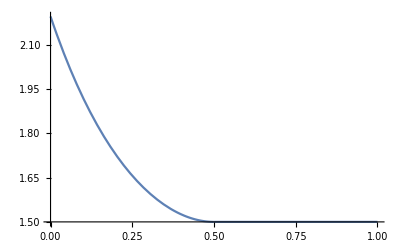

```mathematica
Plot[ ratioPFtangentOverMax[ {0, 0}, xF ], {xF, 0, 1} ]
```

```mathematica
Table[ {xF, ratioPFtangentOverMax[ {0, 0}, xF ]}, {xF, {0.0001, 0.1, 0.25, 0.3, 0.4, 0.5, 0.75, 0.9999}}] // MatrixForm
```

(0.0001 | 2.19582
0.1 | 1.91928
0.25 | 1.65659
0.3 | 1.59999
0.4 | 1.52541
0.5 | 1.5
0.75 | 1.5
0.9999 | 1.5)

```mathematica
0.5 - xAtMaxDisplacementPF[ {0, 0}, 0. ]
xAtMaxDisplacementPF[ {0, 0}, 0.5 ]
0.5 - xAtMaxDisplacementPF[ {0, 0}, 0.25 ]
```

0.0773503

0.5

0.059017

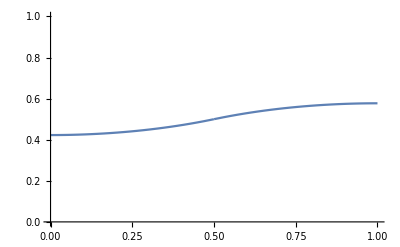

```mathematica
Plot[  xAtMaxDisplacementPF[ {0, 0}, xF ], {xF, 0, 1}, PlotRange -> {0, 1} ]
```

```mathematica
Manipulate[ 
Graphics[ 
{
Gray,
Line[ {{0, 0}, {1, 0}} ],
Black,
Thickness[0.008],
Line[ Table[ {x, 2^log2amp beamDeformedPFDisplacement[x,{kL, kR}, xF ]}, {x, 0, 1, 1/30} ] ],
Line[ { {0, 0}, {xAtMaxDisplacementPF[ {kL, kR}, xF ], 2^log2amp tangentBeamDeformedPFDisplacement[ xAtMaxDisplacementPF[ {kL, kR}, xF ], {kL, kR}, xF ]} } ],
HalfLine[ {{xAtMaxDisplacementPF[ {kL, kR}, xF ], 0}, {xAtMaxDisplacementPF[ {kL, kR}, xF ], -1}}]
}, PlotRange -> { {0, 1}, {-1.1, 0.1}}, Axes -> True, 
FrameTicks -> {Automatic, Range[ -1, 0, 0.05]}, GridLines -> {Automatic, Range[ -1, 0, 0.05]}, Frame -> True,
PlotLabel -> Grid[ {{2^log2amp beamDeformedPFDisplacement[xAtMaxDisplacementPF[ {kL, kR}, xF ],{kL, kR}, xF ]},
{2^log2amp tangentBeamDeformedPFDisplacement[ xAtMaxDisplacementPF[ {kL, kR}, xF ], {kL, kR}, xF ]}} ] ],

{{kL, 0}, 0, 5, 0.25},
{{kR, 0}, 0, 5, 0.25},
{{xF, 0.5}, 0.05, 0.95, 0.05},
Delimiter,
{{log2amp, 3}, 0, 10, 0.1}
]
```

#### fixed-fixed

```mathematica
0.5 - xAtMaxDisplacementPF[ {10^9, 10^9}, 0. ]
xAtMaxDisplacementPF[ {10^9, 10^9}, 0.5 ]
0.5 - xAtMaxDisplacementPF[ {10^9, 10^9}, 0.25 ]
```

0.166667

0.5

0.1

```mathematica
Table[ {xF, NumberForm[ 0.5 - xAtMaxDisplacementPF[ {10^9, 10^9}, xF ] // N,{4, 3}]}, {xF, {0, 0.1, 0.2, 0.25, 0.3, 0.4, 0.5}}]  // Chop // MatrixForm
```

(0 | 0.167
0.1 | 0.143
0.2 | 0.115
0.25 | 0.100
0.3 | 0.083
0.4 | 0.045
0.5 | 0.000)

```mathematica
Table[ {xF, NumberForm[ beamDeformedPFInflection[ {∞, ∞}, xF ] // N,{4, 3}] },{xF, {0, 0.1, 0.2, 0.25, 0.3, 0.4, 0.5}} ]  // Chop // MatrixForm
```

(0 | {0.000,0.667}
0.1 | {0.083,0.679}
0.2 | {0.143,0.692}
0.25 | {0.167,0.700}
0.3 | {0.188,0.708}
0.4 | {0.222,0.727}
0.5 | {0.250,0.750})

```mathematica
Plot[  xAtMaxDisplacementPF[ {0, 0}, xF ], {xF, 0, 1}, PlotRange -> {0, 1} ]
```

-Graphics-

```mathematica
Manipulate[ 
Graphics[ 
{
Gray,
Line[ {{0, 0}, {1, 0}} ],
Black,
Thickness[0.008],
Line[ Table[ {x, 2^log2amp beamDeformedPFDisplacement[x,{kL, kR}, xF ]}, {x, 0, 1, 1/30} ] ],
Line[ { {0, 0}, {xAtMaxDisplacementPF[ {kL, kR}, xF ], 2^log2amp tangentBeamDeformedPFDisplacement[ xAtMaxDisplacementPF[ {kL, kR}, xF ], {kL, kR}, xF ]} } ],
HalfLine[ {{xAtMaxDisplacementPF[ {kL, kR}, xF ], 0}, {xAtMaxDisplacementPF[ {kL, kR}, xF ], -1}}]
}, PlotRange -> { {0, 1}, {-1.1, 0.1}}, Axes -> True, 
FrameTicks -> {Automatic, Range[ -1, 0, 0.05]}, GridLines -> {Automatic, Range[ -1, 0, 0.05]}, Frame -> True,
PlotLabel -> Grid[ {{2^log2amp beamDeformedPFDisplacement[xAtMaxDisplacementPF[ {kL, kR}, xF ],{kL, kR}, xF ]},
{2^log2amp tangentBeamDeformedPFDisplacement[ xAtMaxDisplacementPF[ {kL, kR}, xF ], {kL, kR}, xF ]}} ] ],

{{kL, 0}, 0, 5, 0.25},
{{kR, 0}, 0, 5, 0.25},
{{xF, 0.5}, 0.05, 0.95, 0.05},
Delimiter,
{{log2amp, 3}, 0, 10, 0.1}
]
```

## Old stuff

```mathematica
{fM1, fV1, fu1} = {M, V, u} /. DSolve[ {M'[x] == V[x], V'[x] == -q, M[x] == EI u''[x], u[0] == 0, u[L] == 0, M[0] == 0, M[L] == 0}, {M, V, u}, x ][[1]]
```

{Function[{x},1/2 (L q x-q x^2)],Function[{x},1/2 (L q-2 q x)],Function[{x},(-L^3 q x+2 L q x^3-q x^4)/(24 EI)]}

```mathematica
fu1[L/2] / (fu1'[0] * L/2) // N
```

0.625

```mathematica
{fM2, fV2, fu2} = {M, V, u} /. DSolve[ {M'[x] == V[x], V'[x] == -q, M[x] == EI u''[x], u[0] == 0, u[L] == 0, u'[0] == 0, u'[L] == 0}, {M, V, u}, x ][[1]]
```

{Function[{x},1/12 (-L^2 q+6 L q x-6 q x^2)],Function[{x},1/2 (L q-2 q x)],Function[{x},(-L^2 q x^2+2 L q x^3-q x^4)/(24 EI)]}

```mathematica
xI = x /. Solve[ {fM2[x] == 0, 0 < x < L/2}, x ][[1]] // Simplify[ #, L > 0 ]&
```

-1/6 (-3+√3) L

```mathematica
InterpolatingPolynomial[ {{0, 0}, {L/2, fu2[L/2]} }, x ] // Expand
```

-(L^3 q x)/(192 EI)

```mathematica
(-(L^3 q x)/(192 EI) /.x -> xI )
```

((-3+√3) L^4 q)/(1152 EI)

```mathematica
(-(L^3 q x)/(192 EI) /.x -> xI ) / fu2[ xI] // FullSimplify // PowerExpand // N
```

0.950962

```mathematica
{fM3[x_], fV3[x_], fu3[x_, q_, EI_, L_, kL_, kR_ ]} = {M[x], V[x], u[x]} /. DSolve[ {M'[x] == V[x], V'[x] == -q, M[x] == EI u''[x], u[0] == 0, u[L] == 0, kL u'[0] == M[0], -kR u'[L] == M[L]}, {M, V, u}, x ][[1]];
```

```mathematica
NSolve[ {Derivative[ 2, 0, 0, 0, 0, 0][fu3 ][x, 1, 1, 1, 1, 1 ] == 0, 0 < x < 1/2}, x ]
```

{{x→0.0590414}}

```mathematica
fxI[ kLn_, kRn_ ]  := x /. NSolve[ {Derivative[ 2, 0, 0, 0, 0, 0][fu3 ][x, 1, 1, 1, 1, 1 ] == 0, 0 < x < 1/2}, x ][[1]]
```

```mathematica
InterpolatingPolynomial[ {{0, 0}, {1/2, fu3[1/2]/. {q -> 1, L -> 1, EI -> 1, kL -> kLn, kR -> kRn} } }, x ] // Expand
```

2 x fu3[1/2]

```mathematica
myRatio[ kLn_, kRn_ ] := (-(5 x)/(16 (12+4 kLn+4 kRn+kLn kRn))-(kLn x)/(24 (12+4 kLn+4 kRn+kLn kRn))-(kRn x)/(24 (12+4 kLn+4 kRn+kLn kRn))-(kLn kRn x)/(192 (12+4 kLn+4 kRn+kLn kRn))  /. x -> fxI[kLn, kRn] ) / ( fu3[ fxI[ kLn, kRn], 1, 1, 1, 1, 1 ] )
```

```mathematica
Table[ myRatio[ kL, kR ], {kL, 0.01, 3.01, 0.5}, {kR, 0.01, 3.0, 0.5} ] // MatrixForm
```

(0.916024 | 0.83793 | 0.779299 | 0.73366 | 0.697127 | 0.667221
0.83793 | 0.77019 | 0.718879 | 0.678667 | 0.646304 | 0.619697
0.779299 | 0.718879 | 0.672805 | 0.636511 | 0.60718 | 0.582985
0.73366 | 0.678667 | 0.636511 | 0.603166 | 0.576132 | 0.553772
0.697127 | 0.646304 | 0.60718 | 0.576132 | 0.550893 | 0.529973
0.667221 | 0.619697 | 0.582985 | 0.553772 | 0.529973 | 0.510211
0.642289 | 0.597435 | 0.562685 | 0.53497 | 0.51235 | 0.493538)

```mathematica
(-(5 x)/(16 (12+4 kLn+4 kRn+kLn kRn))-(kLn x)/(24 (12+4 kLn+4 kRn+kLn kRn))-(kRn x)/(24 (12+4 kLn+4 kRn+kLn kRn))-(kLn kRn x)/(192 (12+4 kLn+4 kRn+kLn kRn))  /. x -> fxI[kLn, kRn] )
```

-0.0184505/(12+4 kLn+4 kRn+kLn kRn)-(0.00246006 kLn)/(12+4 kLn+4 kRn+kLn kRn)-(0.00246006 kRn)/(12+4 kLn+4 kRn+kLn kRn)-(0.000307508 kLn kRn)/(12+4 kLn+4 kRn+kLn kRn)

```mathematica
secantLine[ x_, kLn_, kRn_ ] := -((60+8 kRn+kLn (8+kRn)) x)/(192 (4 (3+kRn)+kLn (4+kRn)))
slopeOfSecantLine[ kLn_, kRn_ ] := -(60+8 kRn+kLn (8+kRn))/(192 (4 (3+kRn)+kLn (4+kRn)))
```

```mathematica
With[ {k = k},Table[ {kR, k /. NSolve[ {slopeOfSecantLine[ k, kR ] == Derivative[ 1, 0, 0, 0, 0, 0][fu3 ][0, 1, 1, 1, k, k  ], k > 0}, k ] // N} // Flatten,
{kR, {0, 1, 2, 3, k/4, k/2, k, 2k, 3k, 10^9 k}}] ]
```

{{0,2.34233},{1,3.33333},{2,4.09878},{3,4.71241},{k/4,3.14358},{k/2,4.14911},{k,6.},{2 k,7.89631},{3 k,8.70477},{1000000000 k,10.5498}}

```mathematica
Manipulate[

kLeff = If[ kLinf, 10^9, kLn];
kReff = If[ kRinf, 10^9, kRn];
If[ ampNow === Automatic, amp = -0.5 / fu3[1/2, 1, 1, 1, kLeff, kReff ], amp = ampNow ];

Graphics[ {Line[ Table[ {x, amp fu3[x, 1, 1, 1, kLeff, kReff ]}, {x, 0, 1 , 1/30}] ],
Line[ {{0,0}, {1/2, amp fu3[1/2, 1, 1, 1, kLeff, kReff ] } }],
Disk[ {fxI[kLeff, kReff ], amp fu3[fxI[ kLeff, kReff], 1, 1, 1, kLeff, kReff  ]}, 0.01]}
],
{{kLn, 0}, 0, 3, 0.25},
{{kRn, 0}, 0, 3, 0.25},
{{kLinf, False}, {False, True}},
{{kRinf, False}, {False, True}},
Delimiter,
{{ampNow, 20}, {Automatic, 10, 20, 100, 200}}
]
```

```mathematica
d
```